# Superradiant Proca on Kerr Background

## Initialization

```mathematica
$FKKSRoot = NotebookDirectory[];
$SolutionPath = $FKKSRoot<>"Solutions/";
PlotPath = $FKKSRoot<>"Plots/";
LogFile = $FKKSRoot<>"Logs/LogFile.log";
PlotFileExtension = ".png";
NumberofSlaveKernels = Automatic; (*Default should be Automatic*)

(*Import some helper functions*)
Import[FileNameJoin[{$FKKSRoot, "Packages", "HelperFunctions.wl"}]]

(*Setup xAct definitions*)
Import[FileNameJoin[{$FKKSRoot, "Packages", "xActSetup.wl"}]]

(*Setup Proca Solver*)
Import[FileNameJoin[{$FKKSRoot, "Packages", "KerrWithProca.wl"}]]

(*Import mode overtone worker function for iteration routine*)
Import[FileNameJoin[{$FKKSRoot, "Packages", "ModeOvertoneWorker.wl"}]]

(*Setup Energy Momentum Definitions*)
Import[FileNameJoin[{$FKKSRoot, "Packages", "EnergyMomentum.wl"}]]

(*Setup MST Solver*)
Import[FileNameJoin[{$FKKSRoot, "Packages", "MSTSolver.wl"}]]

(*Setup Inhomogeneous Teukolsky Solver*)
Import[FileNameJoin[{$FKKSRoot, "Packages", "TeukolskySolver.wl"}]]
```

## Proca Equations of Motion Analysis

### Symmetries of Proca Field

```mathematica
DefTensor[A[ζ], ℳ]
sym1 = ContractBasis[LieD[SpacelikeKilling[α],PDsphericalchart]@A[ζ]//ToBasis[sphericalchart], OverDerivatives->True]//Simplify;
sym2 = ContractBasis[LieD[TimelikeKilling[α],PDsphericalchart]@A[ζ]//ToBasis[sphericalchart], OverDerivatives->True]//Simplify;
procafieldsymmetry = {sym1,sym2};
```

### Define Proca Field in FKKS Ansatz

```mathematica
Z = R[r[]]*S[θ[]]*Exp[-I*ω*t[]]*Exp[I*m*ϕ[]];
gradZ = Head[Cd[-ζ]@Z//FromBasisExpand];
FKKSAnsatz = Head[Polarization[ζ,ξ]*gradZ[-ξ]//Simplification];
```

### Separation of Equations of Motion (WIP)

```mathematica
(*To Do*)
```

### Asymptotic Solutions

#### r -> ∞

```mathematica
Block[{DiffAtInfinity, SolAtInfinity},

DiffAtInfinity = Series[(ProcaDiffOpRad@R[r])/((r-(1+Sqrt[1-χ^2]))(r-(1-Sqrt[1-χ^2])))//Simplify, {r,∞,2}]//Normal;
Off[Attributes::notfound];
SolAtInfinity =R[r]/. DSolve[DiffAtInfinity==0, R, r]//First;
On[Attributes::notfound];
SeriesSolAtInfinity=Series[SolAtInfinity, {r,Infinity,1}]//Normal//Simplify;
SeriesSolAtInfinity
]
```

#### r -> r_+

```mathematica
Block[{},
DiffAtHorizon = Series[ProcaDiffOpRad@R[r]//Simplify, {r,1+Sqrt[1-χ^2],1}]//Normal

]
```

```mathematica
ReorganizedODE = Collect[ReorganizedODE//Expand, {R[r], Derivative[1][R][r], Derivative[2][R][r]}];
ODECoefficients = (ReorganizedODE/.c1_*R[r]+c2_*Derivative[1][R][r]+c3_*Derivative[2][R][r]->{c1,c2,c3})/((1+r^2*ν^2)/((-1+r-√(1-χ^2)) (-1+r+√(1-χ^2))))//FullSimplify
ODECoefficientHorizon = Series[ODECoefficients, {r,1+Sqrt[1-χ^2],1}]//Normal//Simplify
ODEAtHorizon = Sum[ODECoefficientHorizon[[i+1]]*Derivative[i][R][r], {i,0,2}];
SolutionAtHorizon = R[r]/.DSolve[ODEAtHorizon==0,R,r]//First;
(Series[SolutionAtHorizon, {r,∞,1}]//Normal)/.Times[x_,y_,z_]->x*y
```

## Solving Proca on Kerr

## Solving the FKKS ansatz

### Parameters

```mathematica
(*Define parameters of numerical calculation*)
ClearAll[ϵ,μNv,μN,νN,ωN,χv,mode,eta,μrange,overtone,polarization,χv,omegaRes,precision,KMax,μ,ν,ω,a,r,branch]
μrange = {5/100, 50/100};
mrange = {1,1};
nrange = {0,0};
δμ = 1/100;
δn=1;
δm=1;

ϵ = 1/10000;
μNv =6/100;
mode = 1;
eta = 0;
overtone = 0;
polarization = -1;
orbitalnumber = mode + polarization;
χv = 995/1000;

BHMass = 1; (*Solar masses*)

omegaRes = 800;
precision = 22;
OptimizationPrecision = 8; (*Precision of function values*)
OptimizationAccuracy = 18; (*Accuracy in location of minima*)
FrequencyInterpolatingOrder = 3;
MaxInterationsMinimization = 10^3;
MaxStepRadialIntegrator = 10^6;
PrecisionGoalRadialIntegrator = 8;
KMax = 4;
branch = 1;

StartingX = ϵ;
EndingX = calcEndingX[<|"m"->mode, "n"->overtone, "μNv"->μNv, "χ"->χv|>];
StartingR = rplusN[χv]+StartingX;
EndingR =  rplusN[χv]+EndingX;

(*Numerical Variables*)
μ = μN/M; ν = νN/M; ω = ωN/M; a = χ*M;

parameters = <|
"μrange"-> μrange,
"δμ"-> δμ,
"nrange"-> nrange,
"δn"->δn,
"mrange"-> mrange,
"δm"->δm,
"EndingX"-> EndingX,
"StartingX"-> StartingX,
"precision"-> precision,
"omegaRes"-> omegaRes,
"FrequencyInterpolatingOrder"->FrequencyInterpolatingOrder,
 "MaxIterationsMinimization"-> MaxInterationsMinimization,
"RadialIntegratorMaxStep"-> MaxStepRadialIntegrator,
"RadialIntegratorPrecisionGoal"-> PrecisionGoalRadialIntegrator,
"OptimizationPrecision"->OptimizationPrecision,
"OptimizationAccuracy"-> OptimizationAccuracy,
"StartingX"->StartingX,
 "EndingX"-> EndingX,
"branch"->branch,
 "KMax"-> KMax,
 "ϵ"-> ϵ,
 "μNv"-> μNv,
 "m"->mode,
"η"-> eta,
 "n"-> overtone,
 "l"-> orbitalnumber,
 "s"-> polarization,
 "χ"-> χv,
"M"-> BHMass
|>;
```

### The Calculation (Single Mass search)

Parameters: μrange→{1/20,1/2} | δμ→1/100 | nrange→{0,0}
δn→1 | mrange→{3,3} | δm→1
EndingX→15555.3 | StartingX→1/10000 | precision→22
omegaRes→800 | FrequencyInterpolatingOrder→3 | MaxIterationsMinimization→1000
RadialIntegratorMaxStep→1000000 | RadialIntegratorPrecisionGoal→8 | OptimizationPrecision→8
OptimizationAccuracy→18 | branch→1 | KMax→4
ϵ→1/10000 | μNv→3/50 | m→1
η→0 | n→0 | l→0
s→-1 | χ→199/200 | M→1

Minimization Results: <|"ω" -> 0.05989096627844203 + 3.411740301918451*^-9*I, "ν" -> -0.06376342330908533 - 1.4388778618242913*^-9*I|>

minimization time: 172.739001

Solution:

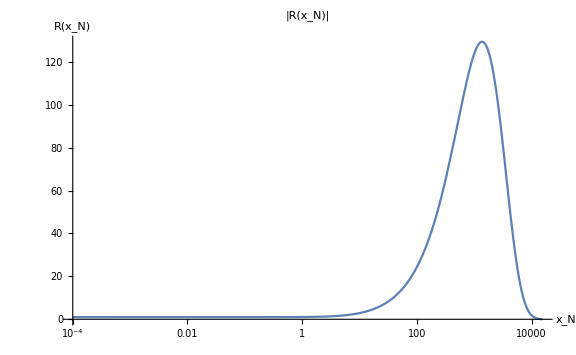
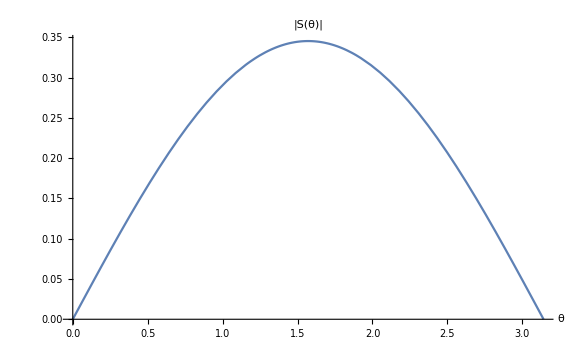
0.0598909662784420303+3.41174030191845105×10^-9 ⅈ
-10818074108/169659556319-(3476654 ⅈ)/2416225930109245
InterpolatingFunction[…]
InterpolatingFunction[…]
{C[0]→1,C[1]→-4.61243×10^-7+1.44215×10^-11 ⅈ,C[2]→7.17105×10^-14-4.48412×10^-18 ⅈ,C[3]→-5.42389×10^-21+5.08729×10^-25 ⅈ,C[4]→2.41594×10^-28-3.01604×10^-32 ⅈ}
0.00361554397535491-5.65149877212991×10^-8 ⅈ
-Graphics-
-Graphics-

```mathematica
(*Turn off irrelevant error messages*)
Off[ClebschGordan::phy];
WatchEvaluation = True;
SaveToDisk = False;

If[omegaNINonRel[parameters]<0,Print["Superradiant condition fails for parameter (μ,m,n,χ,s)=("<>ToString[parameters["μNv"], InputForm]<>","<>ToString[parameters["m"], InputForm]<>","<>ToString[parameters["n"], InputForm]<>","<>ToString[parameters["χ"], InputForm]<>","<>ToString[parameters["s"], InputForm]<>")"];Abort[]];
printData=parameters[[{"ϵ", "μNv", "m", "η", "n", "l", "s", "χ"}]];

Messenger = "";
If[WatchEvaluation,Dynamic[Messenger]]
If[WatchEvaluation,Print[Style["Parameters: ", Bold], Grid[Partition[Table[(parameters//Keys)[[i]] -> (parameters//Values)[[i]], {i,1, Length@parameters}],3], Frame->True]]];
If[WatchEvaluation, Dynamic[RMMessenger]]

(*Minimization using Nelder Mead*)
Messenger=Style["Performing Minimization",Blue, Italic, 24];
minimizetimestart = AbsoluteTime[];
omegaGuess = N[omegaNRNonRel[parameters] + I*omegaNINonRel[parameters]];
nuGuess = getNuValue[omegaGuess, parameters,nuNNonRel[omegaGuess,parameters]]//N;
omegaBoundarySize = 1/2*(omegaNRNonRel[ReplacePart[parameters,"n"->parameters["n"]+1]] - omegaGuess//Re);
omegaBoundary = {omegaGuess - omegaBoundarySize, omegaGuess+omegaBoundarySize};
(*Perform minimization*)
MinimizationResults=RadialMinimize[omegaGuess,  nuGuess, omegaBoundary,  parameters, WatchEvaluation];
If[WatchEvaluation,Print["Minimization Results: "<>ToString[MinimizationResults//N, InputForm]]];
minimizetimestop = AbsoluteTime[];
If[WatchEvaluation,Print["minimization time: "<>ToString[N[minimizetimestop-minimizetimestart], InputForm]]];


(* --------- Solve for kernel of angular matrix --------- *)
Messenger = Row[{ProgressIndicator[Appearance-> "Percolate"],Style["Solving the angular equation for the undetermined coefficients",Blue, Italic, 24]}];
Sfunctemp = Sum[C[k]*SphericalHarmonicY[Abs[parameters["m"]]+2*k+parameters["η"],parameters["m"],θ,ϕ]*Exp[-I*parameters["m"]*ϕ], {k,0,parameters["KMax"]}];
coeffs = SolveAngularSystem[MinimizationResults["ω"], MinimizationResults["ν"],parameters];
Sfunc=FunctionInterpolation[Evaluate[Sfunctemp/.coeffs], {θ,0,π}];

(* --------- Output solution and save to disk --------- *)
TheSolution = <|"ω" -> MinimizationResults["ω"],
			    "ν"->  MinimizationResults["ν"],
		    	"R"-> getRadialSolution[MinimizationResults["ω"], MinimizationResults["ν"], parameters],
		             "S"-> Sfunc,
			    "AngularKernelVector"-> coeffs,
			    "Q"-> QValue[parameters["μNv"], MinimizationResults["ω"]]
			|>;
RadialPlot=LogLinearPlot[
TheSolution["R"][x]//Abs, 
{x,parameters["StartingX"], parameters["EndingX"]}, 
PlotLabel->"|R(x_N)|",
 PlotRange->All,
 AxesLabel->{"x_N", "R(x_N)"},
 ImageSize->Large, 
Epilog-> Inset[Style[Grid[Partition[Table[(parameters//Keys)[[i]] -> (parameters//Values)[[i]], {i,1, Length@parameters}],2], ItemSize->18], 10]]
];
AngularPlot =Plot[
TheSolution["S"][θ]//Abs, 
{θ,0,π}, 
PlotLabel->"|S(θ)|", 
AxesLabel->{"θ", ""},
ImageSize->Large,
Epilog-> Inset[Style[Grid[Partition[Table[(parameters//Keys)[[i]] -> (parameters//Values)[[i]], {i,1, Length@parameters}],2], ItemSize->18], 10]]
];

AppendTo[TheSolution, "RadialPlot"-> RadialPlot];
AppendTo[TheSolution, "AngularPlot"-> AngularPlot];

(*Prepare solution data and write to disk*)
printData=parameters[[{"ϵ", "μNv", "m", "η", "n", "l", "s", "χ"}]];
CacheData = <| "Parameters"-> parameters, "Solution"-> TheSolution|>;
If[WatchEvaluation&&SaveToDisk,Print["Caching results to: RunData_"<>assocToString[printData]]];
If[SaveToDisk,Export[NotebookDirectory[]<>"Solutions/RunData_"<>assocToString[printData]<>".mx", CacheData]]

Messenger=Style["Finished!",Blue, Italic, 24];
Print[Style["\n\n Solution: \n", Blue, Italic, 24]]
Column@(List@@TheSolution)
```

### The Calculation (Serial routine over μ-n-m space)

```mathematica
(*Specify if iterations should produces logs during evaluation that get printed to output*)
WatchEvaluation = True;
TrackIteration=True;
LogRun=True;
SaveToDisk=True;
OverwritePreviousSolutions = True;

(*Display progress bar*)
μIterations =Floor@ ((parameters["μrange"][[2]]-parameters["μrange"][[1]])/parameters["δμ"])+1;
Row[{Style["Progress   ", Bold],ProgressIndicator[Dynamic[μIterationCounter ], {1, μIterations}]}]

(*Initialize various iteration variables and loggers*)
Messenger = "";
ParameterWatcher="";
MinimizationResults="";
KernelsRule = {0->0};
CurrentParameterPoint = {};
CurrentResult = {};

(*instantiate dynamical symbols*)
If[TrackIteration,Dynamic[ParameterWatcher]]
If[WatchEvaluation, Dynamic[RMMessenger]];

μMessenger= " Current μ value: "<>ToString[parameters["μNv"], InputForm];
nMessenger = " Current n value: "<>ToString[parameters["n"], InputForm];
mMessenger = " Current m value: "<>ToString[parameters["m"], InputForm];

(*Begin iterations*)
runStartTime = AbsoluteTime[];
Do[
WorkerFunction[mval, nval, parameters, LogFile,OverwritePrevious -> OverwritePreviousSolutions], 
{mval,parameters["mrange"]//First,parameters["mrange"]//Last},
{nval, parameters["nrange"]//First,parameters["nrange"]//Last}
]

runEndTime=AbsoluteTime[];

Messenger=Style["Finished! Total Time: "<>ToString[N@(Round[runEndTime-runStartTime]/60), InputForm]<>" Minutes",Blue, Italic, 24];
```

Progress

Kernel 0 working on parameter point (μ, m, n) = (3/50, 1 ,0)

Result for Kernel 0: 
	 ω = 0.05989096627844203027983391286907149113`18. + 3.41174030191845104703243279975`18.*^-9*I

Kernel 0 working on parameter point (μ, m, n) = (7/100, 1 ,0)

Result for Kernel 0: 
	 ω = 0.06982629476409225021122906929936829233`18. + 9.38311754254580069892380235605`18.*^-9*I

Kernel 0 working on parameter point (μ, m, n) = (2/25, 1 ,0)

Result for Kernel 0: 
	 ω = 0.07973975445485336886596850152596057314`18. + 2.239464583398036943976800832096`18.*^-8*I

Kernel 0 working on parameter point (μ, m, n) = (9/100, 1 ,0)

Result for Kernel 0: 
	 ω = 0.08962794226451225105834246463952003207`18. + 4.797596568870933461021973922404`18.*^-8*I

Kernel 0 working on parameter point (μ, m, n) = (1/10, 1 ,0)

Result for Kernel 0: 
	 ω = 0.09948735181311416810622440698411754055`18. + 9.439781220944560336885689886865`18.*^-8*I

Kernel 0 working on parameter point (μ, m, n) = (11/100, 1 ,0)

Result for Kernel 0: 
	 ω = 0.10931436405662252735571701723798862773`18. + 1.7340201536409728920876845995468`18.*^-7*I

Kernel 0 working on parameter point (μ, m, n) = (3/25, 1 ,0)

Result for Kernel 0: 
	 ω = 0.11910523863231178616356267068448990067`18. + 3.0096509812947279670064344960361`18.*^-7*I

Kernel 0 working on parameter point (μ, m, n) = (13/100, 1 ,0)

Result for Kernel 0: 
	 ω = 0.12885610608779336237705891898012712269`18. + 4.980726635316034504445552642449`18.*^-7*I

Kernel 0 working on parameter point (μ, m, n) = (7/50, 1 ,0)

Result for Kernel 0: 
	 ω = 0.13856296101764677525741041480644461442`18. + 7.914683987776152678728743508028`18.*^-7*I

Kernel 0 working on parameter point (μ, m, n) = (3/20, 1 ,0)

Result for Kernel 0: 
	 ω = 0.14822165626796868309108464055709998158`18. + 1.21434829641592821352794094245004`18.*^-6*I

Kernel 0 working on parameter point (μ, m, n) = (4/25, 1 ,0)

Result for Kernel 0: 
	 ω = 0.15782789832480034224742901371729792`18. + 1.80696031417750129253410308537982`18.*^-6*I

Kernel 0 working on parameter point (μ, m, n) = (17/100, 1 ,0)

Result for Kernel 0: 
	 ω = 0.16737724406365286107092279473817190727`18. + 2.61708470440269962355801228610704`18.*^-6*I

Kernel 0 working on parameter point (μ, m, n) = (9/50, 1 ,0)

Result for Kernel 0: 
	 ω = 0.17686509899119138823010753088633665902`18. + 3.70021610423971881484535658151266`18.*^-6*I

Kernel 0 working on parameter point (μ, m, n) = (19/100, 1 ,0)

Result for Kernel 0: 
	 ω = 0.18628671727634734172701778392376841402`18. + 5.11974542913319718913603873086622`18.*^-6*I

Kernel 0 working on parameter point (μ, m, n) = (1/5, 1 ,0)

Result for Kernel 0: 
	 ω = 0.19563720359721495605558912364765665062`18. + 6.94664541295091332580984934966809`18.*^-6*I

Kernel 0 working on parameter point (μ, m, n) = (21/100, 1 ,0)

Result for Kernel 0: 
	 ω = 0.20491151712289981788503559105351577625`18. + 9.25894385167446567431979634874467`18.*^-6*I

Kernel 0 working on parameter point (μ, m, n) = (11/50, 1 ,0)

Result for Kernel 0: 
	 ω = 0.21410447777331442357339970127684045526`18. + 0.00001214082281243860739964196563356874`18.*I

Kernel 0 working on parameter point (μ, m, n) = (23/100, 1 ,0)

Result for Kernel 0: 
	 ω = 0.22321077492300046582064654132984869046`18. + 0.0000156813298395684077434046039858748`18.*I

Kernel 0 working on parameter point (μ, m, n) = (6/25, 1 ,0)

Result for Kernel 0: 
	 ω = 0.23222497872116273423743568814411418581`18. + 0.00001997268248174698834330422237628428`18.*I

Kernel 0 working on parameter point (μ, m, n) = (1/4, 1 ,0)

Result for Kernel 0: 
	 ω = 0.24114155413452019352385746731272977189`18. + 0.00002510816798821375118381088864964066`18.*I

Kernel 0 working on parameter point (μ, m, n) = (13/50, 1 ,0)

Result for Kernel 0: 
	 ω = 0.24995487780045835757710750813238134607`18. + 0.00003117964514792927514282337995226935`18.*I

Kernel 0 working on parameter point (μ, m, n) = (27/100, 1 ,0)

Result for Kernel 0: 
	 ω = 0.25865925771288161934871886205673564939`18. + 0.00003827467553915442716381064845734597`18.*I

Kernel 0 working on parameter point (μ, m, n) = (7/25, 1 ,0)

Result for Kernel 0: 
	 ω = 0.26724895572124169051689090556842307662`18. + 0.00004647335474890634021054406024152324`18.*I

Kernel 0 working on parameter point (μ, m, n) = (29/100, 1 ,0)

Result for Kernel 0: 
	 ω = 0.27571821272574665202018626810181306728`18. + 0.00005584492281095791294603609762963048`18.*I

Kernel 0 working on parameter point (μ, m, n) = (3/10, 1 ,0)

Result for Kernel 0: 
	 ω = 0.28406127636655260610188119631573784846`18. + 0.0000664442342164192456386961242675507`18.*I

Kernel 0 working on parameter point (μ, m, n) = (31/100, 1 ,0)

Result for Kernel 0: 
	 ω = 0.29227243096899341025777365895056081997`18. + 0.00007830822403945439920194302537468376`18.*I

Kernel 0 working on parameter point (μ, m, n) = (8/25, 1 ,0)

Result for Kernel 0: 
	 ω = 0.30034602934802227471599698320177901511`18. + 0.00009145252869652682799482397277440347`18.*I

Kernel 0 working on parameter point (μ, m, n) = (33/100, 1 ,0)

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

Result for Kernel 0: 
	 ω = 0.30827652602969190036505037213969923103`18. + 0.00010586839885075422539907108824868247`18.*I

Kernel 0 working on parameter point (μ, m, n) = (17/50, 1 ,0)

Result for Kernel 0: 
	 ω = 0.31605851130905678017107197715492968522`18. + 0.00012152003745414433328978505418243677`18.*I

Kernel 0 working on parameter point (μ, m, n) = (7/20, 1 ,0)

Result for Kernel 0: 
	 ω = 0.32368674558310676847746593609836284051`18. + 0.00013834255049965675020679470992021013`18.*I

Kernel 0 working on parameter point (μ, m, n) = (9/25, 1 ,0)

Result for Kernel 0: 
	 ω = 0.33115619316167901349872605665605464125`18. + 0.00015624065847744687566892615071302072`18.*I

Kernel 0 working on parameter point (μ, m, n) = (37/100, 1 ,0)

Result for Kernel 0: 
	 ω = 0.33846205483810013765356251713456491073`18. + 0.00017508825964686210783571807629178416`18.*I

Kernel 0 working on parameter point (μ, m, n) = (19/50, 1 ,0)

Result for Kernel 0: 
	 ω = 0.34559979838784705151280880832815735353`18. + 0.00019472889674470744208167736510186227`18.*I

Kernel 0 working on parameter point (μ, m, n) = (39/100, 1 ,0)

Result for Kernel 0: 
	 ω = 0.35256518613863909620958733273055022336`18. + 0.00021497719473826947185623931034032514`18.*I

Kernel 0 working on parameter point (μ, m, n) = (2/5, 1 ,0)

Result for Kernel 0: 
	 ω = 0.35935429877305906293507968283996617208`18. + 0.00023562127640410371204211806532791859`18.*I

Kernel 0 working on parameter point (μ, m, n) = (41/100, 1 ,0)

Result for Kernel 0: 
	 ω = 0.36596355434501035900490539056516087927`18. + 0.00025642599364923761613523556100005109`18.*I

Kernel 0 working on parameter point (μ, m, n) = (21/50, 1 ,0)

Result for Kernel 0: 
	 ω = 0.37238972158139085912999771190223432092`18. + 0.00027713671249634685998452141793281448`18.*I

Kernel 0 working on parameter point (μ, m, n) = (43/100, 1 ,0)

Result for Kernel 0: 
	 ω = 0.37862992656894620140475862068344704456`18. + 0.00029748329434029014805881865984727326`18.*I

Kernel 0 working on parameter point (μ, m, n) = (11/25, 1 ,0)

### The Calculation (Parallelized routine over m-n space, serial over μ space)

```mathematica
(*Specify if iterations should produces logs during evaluation that get printed to output*)
WatchEvaluation = True;
TrackIteration=True;
LogRun = True;
SaveToDisk=True;
OverwritePreviousSolutions=False;

(* ----- Prepare logging ----- *)
If[FileExistsQ[LogFile],
DeleteFile[LogFile];
];
CreateFile[LogFile];
Messenger = Row[{ProgressIndicator[Appearance->"Percolate"], "Executing Parameter space iteration"}];
Dynamic[Messenger]

(* ----- Setup Parallelization ----- *)
CloseKernels[];
If[TrueQ[NumberofSlaveKernels==Automatic],
LaunchKernels[Min[$ProcessorCount,(Last@parameters["mrange"] - First@parameters["mrange"] + 1)*(Last@parameters["nrange"] - First@parameters["nrange"] + 1)]];,
LaunchKernels[NumberofSlaveKernels];
];
DistributeDefinitions[parameters, WorkerFunction,$SolutionPath,$FKKSRoot];
ParallelEvaluate[Import[$FKKSRoot<>"Packages/KerrWithProca.wl"]];

(*Setup parallelized watcher*)
KernelsRule = ParallelTable[$KernelID->i, {i,$KernelCount}];
CurrentParameterPoint = ConstantArray[0, $KernelCount];
CurrentResult = ConstantArray[0, $KernelCount];
SetSharedVariable[KernelsRule, CurrentParameterPoint,CurrentResult];
PrintTemporary@Dynamic[CurrentParameterPoint//Column];
PrintTemporary@Dynamic[CurrentResult//Row];

(*Turn off irrelevant error messages*)
Off[ClebschGordan::phy];ParallelEvaluate[Off[ClebschGordan::phy]];
Off[NMinimize::nnum];ParallelEvaluate[Off[NMinimize::nnum]];



(* ----- Execute Parallelized Iterations ----- *)
runStartTime = AbsoluteTime[];
(Evaluators = Flatten@Table[ParallelSubmit[{mv, nv},WorkerFunction[mv,nv, OverwritePrevious -> OverwritePreviousSolutions]], 
			{nv, parameters["nrange"]//First, parameters["nrange"]//Last}, 
			{mv, parameters["mrange"]//First, parameters["mrange"]//Last}
			])//Partition[#, ($KernelCount)/2//Floor]&//Grid
WaitAll[Evaluators]


runEndTime=AbsoluteTime[];
Messenger=Style["Finished! Total Time: "<>ToString[N@(Round[runEndTime-runStartTime]/60), InputForm]<>" Minutes",Blue, Italic, 24];
(*Clean up*)
CloseKernels[];
```

## Analyzing the solutions

### Import Data

```mathematica
AllProcaSolutions = getResults[$SolutionPath];
μOrderingIndex = Ordering@AllProcaSolutions[[All, "Parameters", "μNv"]];
AllProcaSolutions = AllProcaSolutions[[μOrderingIndex]];

ωvalues = AllProcaSolutions[[All, "Solution", "ω"]];
νvalues = AllProcaSolutions[[All, "Solution", "ν"]];
μvalues = AllProcaSolutions[[All, "Parameters", "μNv"]];
mvalues = AllProcaSolutions[[All, "Parameters", "m"]];
nvalues = AllProcaSolutions[[All, "Parameters", "n"]];
angularcoeffs = Table[C[i], {i,0,4}]/.#&/@AllProcaSolutions[[All, "Solution","AngularKernelVector"]];
```

### Plot Data

#### ω_R/μ vs μ

```mathematica
nmin = 0; nmax =  4; mmin= 1; mmax= 4;
DataCollection = Association@@(Table[
(ωvs = OvertoneModeGroup[ni,mi, AllProcaSolutions][[All, "Solution", "ω"]];
μvs = OvertoneModeGroup[ni,mi,AllProcaSolutions][[All, "Parameters", "μNv"]];
"n"<>ToString[ni]<>"m"<>ToString[mi]-> Thread[{μvs, (Re@ωvs)/μvs}]
), {ni, nmin,nmax}, {mi, mmin,mmax}]//Flatten[#,1]&);
OmegaRMuRelativePlots = Row[Flatten@{

Table[
ListPlot[
Table[DataCollection["n"<>ToString[i]<>"m"<>ToString[Μ]], {i, nmin, nmax}], 
ImageSize->{500,350}, 
PlotLabels->Table["n="<>ToString[i]<>"  m="<>ToString[Μ],  {i, nmin,nmax}],
PlotRange->All,
Frame-> True,
FrameLabel->{"μ_N", None},
Epilog->Inset[Framed@Style["ω_real/μ",20], {0.1,Center}]
], 
{Μ, mmin,mmax}
],
ListPlot[
Table[DataCollection["n0m"<>ToString[i]], {i, mmin,mmax}]//Select[#, Not[EmptyQ[#]]&]&,
 ImageSize->{500,350}, 
PlotLabels->Table["n="<>ToString[0]<>"  m="<>ToString[i],  {i, mmin, mmax}],
PlotRange->{(ωvalues/μvalues//Re//Min)-0.05,1.},
Frame-> True,
FrameLabel->{"μ_N", None},
Epilog->Inset[Framed@Style["ω_real/μ",20], {0.1,Center}]
],
ListLinePlot[
Flatten[Table[DataCollection["n"<>ToString[j]<>"m"<>ToString[i]], {i, mmin,mmax}, {j, nmin, nmax}],1]//Select[#, Not[EmptyQ[#]]&]&,
 ImageSize->{500,350}, 
PlotLabels->Flatten[Table["n="<>ToString[j]<>"  m="<>ToString[i],  {i, mmin, mmax}, {j,nmin, nmax}],1],
PlotRange->{(ωvalues/μvalues//Re//Min)-0.05,1.},
Frame-> True,
FrameLabel->{"μ_N", None},
Epilog->Inset[Framed@Style["ω_real/μ",20], {0.1,Center}]
]
}]
Export[PlotPath<>"OmegaRMuRelative"<>PlotFileExtension, OmegaRMuRelativePlots];
```

#### ω_I vs μ

```mathematica
nmin = 0; nmax =  4; mmin= 1; mmax= 4;
DataCollection = Association@@(Table[
(ωvs = OvertoneModeGroup[ni,mi,AllProcaSolutions][[All, "Solution", "ω"]];
μvs = OvertoneModeGroup[ni,mi,AllProcaSolutions][[All, "Parameters", "μNv"]];
"n"<>ToString[ni]<>"m"<>ToString[mi]-> Thread[{μvs, Im@ωvs}]
), {ni, nmin,nmax}, {mi, mmin,mmax}]//Flatten[#,1]&);

OmegaIMuPlots = Row@Table[
ListLogPlot[KeySelect[DataCollection, StringContainsQ["m"<>ToString[Μ]]],
ImageSize->Large,
AxesLabel->{"μ", "Mω_I"},
Epilog->Inset[Framed[Style["ω_I", Black, 32]], {0.25, Automatic}]
], 
{Μ, mmin,mmax}
]
Export[PlotPath<>"OmegaIMu"<>PlotFileExtension, OmegaIMuPlots];
```

#### Angular Matrix Kernel Vector

```mathematica
AngularCoeffPlot = ListLinePlot[
angularcoeffs//Abs//Log10, 
Frame->True,
FrameLabel->{"Index", "Log(C_i)"},
RotateLabel->False,
FrameTicks->{{Automatic,None},{Table[i, {i,1, Length@angularcoeffs[[1]]}], Automatic}}, 
PlotRange->{{1, All},{All,All}},
Epilog->Inset[Framed[Style["Angular Matrix Kernel Coefficients", Black]], {1.7, -15}]
];
Export[PlotPath<>"AngularMatrixKernelVector"<>PlotFileExtension, AngularCoeffPlot];
```

#### Angular Function

```mathematica
ParallelDo[
func = (AllProcaSolutions//Select[#, #["Parameters", "m"]==i&]&)[[All, "Solution", "S"]];
funcMax = (#[π/2]&/@func)//Re//Max//N//SetPrecision[#,6]&;
funcMin = (#[π/2]&/@func)//Re//Min//N//SetPrecision[#,6]&;
funcAngularPlot = Plot[Table[func[[i]][θ], {i,1,Length@func}]//Re, {θ,0,π}, 
					PlotLabel-> "S(θ)",
					Ticks->{{0, π/2, π}, Automatic},
					AxesLabel->{"θ", Automatic},
					ImageSize->Large,
					Epilog->{Inset[
								Plot[Table[func[[i]][θ], {i,1,Length@func}]//Re,
									 {θ,999/2000 π, 1001/2000*π},
									 Frame->True,
									 PlotRange->All,
									ImageSize->Small,
									FrameTicks->{{{funcMin, funcMax}, None}, {{999/2000 π, 1001/2000*π}, None}}
									],
								 {Center, funcMax/2}],
							Circle[{π/2, funcMax},{(π/2)/18, 0.02}],
							Arrow[{{π/2, Sign[funcMax]*((funcMax//Abs) -0.02)}, {π/2,Sign[funcMax]*((funcMax//Abs) -0.1)}}]
							}
					];

Export[PlotPath<>"AngularFuncm"<>ToString[i]<>PlotFileExtension, funcAngularPlot],
{i,Min[mvalues], Max[mvalues]}
]
```

#### Radial Function

```mathematica
sample = Table[(Select[OvertoneModeGroup[i,2, AllProcaSolutions], #["Parameters"]["μNv"]==17/100&]//First)["Solution","R"], {i,Min[nvalues], Max[nvalues]}];
RadialPlots = Row[
		Table[
		LogLinearPlot[
			Callout[sample[[i]][r]//Abs,
				       "n="<>ToString[Sort[DeleteDuplicates[nvalues]][[i]]], 
					Above
				],
			{r,10, sample[[i]]["Domain"]//Max}, 
			PlotRange->All,
			PlotStyle->Black,
			ImageSize->Medium,
			PlotLabel->"R(x)",
			Frame-> True,
			FrameLabel->{"x", None},
			PlotTheme->"Scientific"
			], 
		{i,1, Length@sample}
		]//Append[#,Graphics[Text[Framed[Style["μNv=17/100\n m = 2",15], ImageSize->Medium]], ImageSize->Medium]]&, 
Spacer[2]
]
Export[PlotPath<>"RadialSamples"<>PlotFileExtension, RadialPlots];
```

## Black Hole Evolution

## Sample Data

```mathematica
SampleSolutionSets = {
					(*{{"m",1}, {"n",0}, {"μNv", "1_4"}},
					{{"m",1}, {"n",0}, {"μNv", "13_50"}},
					{{"m",1}, {"n",0}, {"μNv", "27_100"}},
					{{"m",1}, {"n",0}, {"μNv", "7_25"}},
					{{"m",1}, {"n",0}, {"μNv", "29_100"}},*)
					{{"m",1},{"n",0},{"μNv","3_10"}}
				};

SampleData = First[getResults[$SolutionPath,#]]&/@SampleSolutionSets;
```

## Normalization

Normalize the proca field such that the total energy of the proca cloud corresponds to the reduction in energy of the Kerr black hole

```mathematica
Normalizations =FKKSNormalization[#,1,Recalculate->True]&/@SampleData;
NormedData =Table[RenormalizeProcaSolution[SampleData[[i]],Normalizations[[i]]["Normalization"]], {i,1,Length@SampleData}];
FinalMasses = Normalizations[[All, "FinalMass"]];
FinalSpins = Normalizations[[All, "FinalSpin"]];
Normalization = Normalizations[[All,"Normalization"]]
TotalEnergy=Normalizations[[All, "TotalEnergy"]]
```

## Gravitational Radiation from Proca Cloud

## Asymptotic Flux

Calculate the modal decomposition of the Teukolsky Source Term
𝒯_lmω = ∫dΩdt ρ^-5(ρ̄)^-1 2*𝒯*(e^(-imϕ + iωt))_-2 S_lm^aω

```mathematica
orbitalnumber = 2;
modenumber = 2;
AllTlmw = TeukolskySourceModal[#,orbitalnumber,modenumber, Recalculate->True]&/@NormedData;
```

Calculate the asymptotic amplitude 
(Z^*)_lmω = 1/(2(iωB^inc)_lmω)∫_(r_+)^∞ ⅆr(𝒯_lmω(r) * R_lmω^in(r))/(Δ^2(r))

```mathematica
PrintTemporary@Dynamic[$Messenger];
Block[{$MSTMaxN=15},
AsymptoticAmplitudes = Table[TeukolskyZInfinity[NormedData[[i]],AllTlmw[[i]],2,2], {i,1,Length@SampleData}]
]
```

From the modal decomposition of the NP scalar ψ_4, we derive the asymptotic flux as
(dE/dt)_lmn= (|Z_lmω|^2)/(4(π(ω_n))^2)
and the total emitted flux is
(dE/dt) =(Σ_{l,m,n}(dE/dt))_lmn

```mathematica
AsymptoticFluxes = Table[EnergyFlux[NormedData[[i]],2,2, TeukolskyTlmw->AllTlmw[[i]], ZCoefficient->AsymptoticAmplitudes[[i]]], {i,1,Length@SampleData}]
NormalizedAsymptoticFluxes = AsymptoticFluxes/(1-FinalMasses)^2
```

## Analysis of Solutions

Import all data

```mathematica
AllData = Import/@FileNames[All, $SolutionPath][[1;;450]];
SampleData = AllData;
```

Partition data

```mathematica
n0m1Data = OvertoneModeGroup[0,1,AllData];
n0m1Fluxes = n0m1Data[[All, "Derived", "Einf"]];
n0m1TotalEn = n0m1Data[[All, "Derived", "Normalization", "TotalEnergy"]];
n0m1Masses = n0m1Data[[All, "Parameters", "μNv"]];
```

Energy vs Mass

```mathematica
Thread[{n0m1Masses, n0m1TotalEn}]//ListLogPlot
```

Mass vs Rescaled Flux

```mathematica
Thread[{n0m1Masses,n0m1Fluxes/n0m1TotalEn}]//ListLogPlot
```